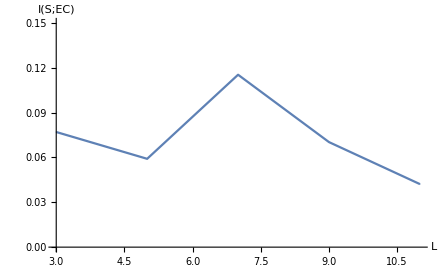

file.pdf

```mathematica
SetDirectory[NotebookDirectory[]];
s=Import["results_error_bars_inc.xlsx"][[1]];
sNames=s[[1]];
sData=s[[2;;]];
Data=Apply[Around,Transpose[{sData[[;;,2]],sData[[;;,3]]}],1];
DataPlot=Transpose[{sData[[;;,1]],Data}];
plot=ListLinePlot[DataPlot,AxesLabel->{"L","I(S;EC)"},PlotRange->{{3,11},{0,0.15}}]
Export["file.pdf",plot]
```